# Vandermonde Matrix

```mathematica
n=10;
z=Range[0.1,1,0.01];
X=Transpose[Table[LegendreP[i,2z-1],{i,0,n}]];
```

```mathematica
M=Dot[Transpose[X],X];
MatrixForm[Dot[Inverse[M],M]]
```

```mathematica
LUDecomposition[M][[3]]
```

1338.58

# Smoothing Penalty

```mathematica
n=10;
e=Table[0,n+1];
With[{value=Sum[c[i]LegendreP[i,2x-1],{i,0,n}],controls=Sequence@@Table[{{c[i],e[[i+1]]},-1,1,Appearance->"Labeled"},{i,0,n}]},Manipulate[Show[Plot[value,{x,0,1},PlotRange->{-0.1,1},PlotLabel->ScientificForm[Expand[value],1],ImageSize->Large,PlotLegends->Placed[Integrate[D[value,{x,2}]^2,{x,0,1}],Below]]],controls]]
```

# Wage Data

```mathematica
wage=Import["/Users/jameschok/Desktop/wage_scaled.csv", "Data","HeadLiners"->1];
```

```mathematica
ListPlot[wage]
```

### L2-Regularization

```mathematica
n=10;
X=Transpose[Table[(wage[[All,1]]+Boole[i==0])^i,{i,0,n}]];
y=wage[[All,2]];
fits=<||>;
For[i=-4,i<=0,i++,fits[10^i]=Dot[Inverse[Dot[Transpose[X],X]+10^i IdentityMatrix[n+1]],Transpose[X],y]];
```

```mathematica
lambdas=Table[10^i,{i,-4,0}];
```

```mathematica
polynomialFits=Table[Sum[fits[10^i][[k+1]] x^k,{k,0,n}],{i,-4,0}];
```

```mathematica
Manipulate[Show[Plot[polynomialFits[[i]],{x,0,1},PlotLegends->Placed[StringJoin["λ=",ToString[N[lambdas[[i]]]],", Wiggle=",ToString[Integrate[D[polynomialFits[[i]],{x,2}]^2,{x,0,1}]]],Below],ImageSize->Large,PlotRange->{0,1},PlotLabel->NumberForm[polynomialFits[[i]],3]],ListPlot[wage]],{i,{1,2,3,4,5}}]
```

```mathematica
fits
```

```mathematica
Table[i,{i,1,7}]
```

{1,2,3,4,5,6,7}

### Legendre Polynomials

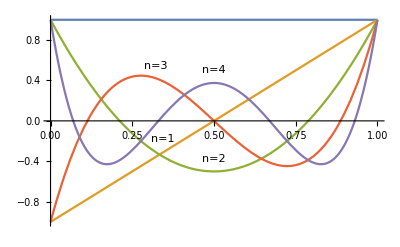

```mathematica
MyLegendre=Table[LegendreP[n,2x-1],{n,0,4}];
Plot[MyLegendre,{x,0,1},PlotLabels->Placed[{"n=0","n=1","n=2","n=3","n=4"},{{Scaled[0.5],Above},{Scaled[0.385],Above}}]]
```

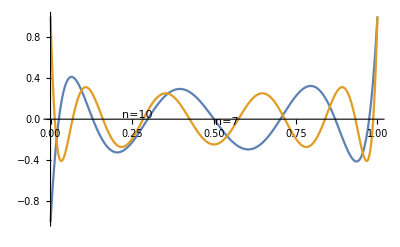

```mathematica
MyLegendre=Table[LegendreP[n,2x-1],{n,{7,10}}];
Plot[MyLegendre,{x,0,1},PlotLabels->Placed[{"n=7","n=10"},{{Scaled[0.5],Above},{Scaled[0.385],Above}}]]
```

### High/Low-pass filter

```mathematica
n=5;
X=Transpose[Table[LegendreP[i,2wage[[All,1]]-1],{i,0,n}]];
y=wage[[All,2]];
e=Dot[Inverse[Dot[Transpose[X],X]],Transpose[X],y];
With[{value=Sum[c[i]LegendreP[i,2x-1],{i,0,n}],controls=Sequence@@Table[{{c[i],e[[i+1]]},-1,1,Appearance->"Labeled"},{i,0,n}]},Manipulate[Show[Plot[value,{x,0,1},PlotRange->{-0.1,1},PlotLabel->ScientificForm[Expand[value],1],ImageSize->Large,PlotLegends->Placed[Integrate[D[value,{x,2}]^2,{x,0,1}],Below]],ListPlot[wage]],controls]]
```

```mathematica
ParametricPlot3D[{2 Cos[u] Cos[v],2 Cos[u] Sin[v], Sin[u]/2},{u,-Pi/2,Pi/2},{v,0,2 Pi},AxesLabel->{Subscript[c, 1],Subscript[c, 2],Subscript[c, 3]}]
```

# Sobolev Smoothing

```mathematica
n=10;
X=Transpose[Table[LegendreP[i,2wage[[All,1]]-1],{i,0,n}]];
y=wage[[All,2]];
fits=<||>;
For[i=-4,i<=0,i++,fits[10^i]=Dot[Inverse[Dot[Transpose[X],X]+10^i DiagonalMatrix[Table[(m+Boole[m==0])^m,{m,0,n}]]],Transpose[X],y]];
```

```mathematica
legendreFits=Table[Sum[fits[10^k][[i+1]]LegendreP[i,2x-1],{i,0,n}],{k,-4,0}];
```

```mathematica
lambdas=Table[10^i,{i,-4,0}];
```

```mathematica
Manipulate[Show[Plot[legendreFits[[k]],{x,0,1},PlotLegends->Placed[StringJoin["λ=",ToString[N[lambdas[[k]]]],", Wiggle=",ToString[Integrate[D[legendreFits[[k]],{x,2}]^2,{x,0,1}]]],Below],ImageSize->Large,PlotRange->{0,1}],ListPlot[wage]],{k,{1,2,3,4,5}}]
```

```mathematica
fits
```

```mathematica
n=10;
X=Transpose[Table[LegendreP[i,2wage[[All,1]]-1],{i,0,n}]];
y=wage[[All,2]];
e=Dot[Inverse[Dot[Transpose[X],X]+0.0001DiagonalMatrix[Table[(m+Boole[m==0])^m,{m,0,n}]]],Transpose[X],y];
```

```mathematica
Plot[Sum[e[[i+1]]LegendreP[i,2x-1],{i,0,n}],{x,0,1}]
```